# HW 3: Astro 735

## Elijah Bernstein-Cooper

#### 1a

Given the Friedman equation
	a'(a_):=a H0 √((a0^3 Ωm0)/a^3+(a0^2 Ωk0)/a^2+ΩΛ0);
we can find the minimum of a'(a)  by taking the derivate with respect to a
	a''(a_):=(∂a'(a))/(∂a);
	Simplify[(∂a'(a))/(∂a)] = (2 a^3 H0 ΩΛ0-a0^3 H0 Ωm0)/(2 a^3 √((a0^3 Ωm0)/a^3+(a0^2 Ωk0)/a^2+ΩΛ0))
and solving for a when a''(a) =0
	a_min:=Solve[a''(a)==0,a]
where a_min is
	a→-((-1/2)^(1/3) a0 Ωm0^(1/3))/ΩΛ0^(1/3), or a→(a0 Ωm0^(1/3))/(2^(1/3) ΩΛ0^(1/3)) or a→((-1)^(2/3) a0 Ωm0^(1/3))/(2^(1/3) ΩΛ0^(1/3))
We know that a cannot be negative, thus 
	a_min→(a0 Ωm0^(1/3))/(2^(1/3) ΩΛ0^(1/3))
is the only solution.

#### 1b

Plugging a_min into the Friedman equation we get
	a_min'(a):=a_min H0 √((a0^3 Ωm0)/a^3+(a0^2 Ωk0)/a^2+ΩΛ0);
which we can simplify algebraically in mathematica
	Simplify[(a_min'(a))^2/. a_min]
Giving us
	a_min^2 H0^2 ((2^(2/3) Ωk0 ΩΛ0^(2/3))/Ωm0^(2/3)+3 ΩΛ0)

#### 1c

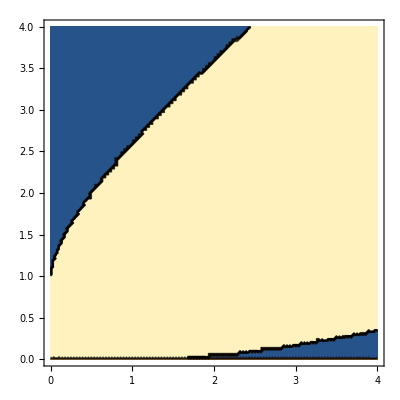

```mathematica
ContourPlot[Sign[3*ΩΛ0+Ωk0*((2*ΩΛ0)/Ωm0)^(2/3)/.{Ωk0->1-(ΩΛ0+Ωm0)}],{Ωm0,0,4},{ΩΛ0,0,4}]
```

The plot above shows the sign of the argument 3ΩΛ0+Ωk((2ΩΛ0)/Ωm0)^(2/3) where the y axis is ΩΛ0 and the x axis is Ωm0, blue is negative and yellow is positive. When this argument is negative, the universe is closed. For parameter values in the top-left corner, the space of the universe will have started as in the Big Bang, starting from a point source, expanding to a maximum, then contracting back to a point source. For parameter values in the bottom-right corner, the space of the universe will start as infinite, contract to a minimum, and expand to back to infinity.

#### 2a

We can solve for the frequency, ν_max, which maximizes the Blackbody function B(T,ν)
	B(T,ν)=(2 h ν^3)/(c^2 (exp((h ν)/(k T))-1))
by setting the derivative with respect to ν of the blackbody function 
	(∂B(T,ν))/(∂ν)=(2 h ν^2 (-3 (-1+ⅇ^((h ν)/(k T))) k T+ⅇ^((h ν)/(k T)) h ν))/(c^2 (-1+ⅇ^((h ν)/(k T)))^2 k T)
equal to 0 and solving for ν_max. We complete this with mathematica
	ν_max=NSolve[(∂B(T,ν))/(∂ν)==0,ν]
	ν_max=(2.82144 k T)/h

#### 2b

We can determine the doppler shifted temperature of the CMB due to the Sun's peculiar velocity by using the Doppler equation
	ν=ν_0(Δv/c+1)
where ν_0 is the rest frequency of the observed light, and Δv is the difference in velocity between the observer and the emitter, 30 Mcm/s.
ν_0=ν_max where T→2.72548,h→6.62 10^10,k→1.38 10^16
The observed frequency will be 
	ν=1.603×10^6  s^-1
and using ν in Wein's law we can solve for the temperature
	T→2.72821
which is only on part in one thousand difference.

3a

In a spatially flat universe we solved for the evolution of time from the Friedman equation
	t=(2 log(√((a^3 ΩΛ0)/Ωm0)+√((a^3 ΩΛ0)/Ωm0+1)))/(3 (H0 √ΩΛ0))
We can write this in a more elegent form by first defining
	tanθ = (Ωm0/ΩΛ0)^(1/2)(1+z)^(3/2)
Given the form
	(1 + cosθ)/sinθ = 1/sinθ+cosθ/sinθ
		=cscθ+cotθ
		=√(1+cot^2 θ)+cotθ
which has the same form as 
	√((a^3 ΩΛ0)/Ωm0+1)+√((a^3 ΩΛ0)/Ωm0)
thus 
	t=(2 log((1 + cosθ)/sinθ))/(3 (H0 √ΩΛ0))
3b

The present age of the universe, t_0 will be when the redshift z is 0, or a = 1, thus	
	θ = (arctan(Ωm0/ΩΛ0))^(1/2)
and 
	
	t=(2 log((1 + cos((arctan(Ωm0/ΩΛ0))^(1/2)))/(sin((arctan(Ωm0/ΩΛ0))^(1/2)))))/(3 (H0 √ΩΛ0))
with the identities
	sin(arctan(x)) = x/(√(1+x^2))        and       cos(arctan(x)) = 1/(√(1+x^2))
then
	cos(arctan((Ωm0/ΩΛ0)^(1/2))) = 1/(√(1 + (Ωm0/ΩΛ0)^(1/2)))
	sin(arctan((Ωm0/ΩΛ0)^(1/2))= (Ωm0/ΩΛ0)^(1/2)/(√(1 + (Ωm0/ΩΛ0)^(1/2)))
	(1 + cos((arctan(Ωm0/ΩΛ0))^(1/2)))/(sin((arctan(Ωm0/ΩΛ0))^(1/2)))= (1+1/(√(1 + (Ωm0/ΩΛ0)^(1/2))))/((Ωm0/ΩΛ0)^(1/2)/(√(1 + (Ωm0/ΩΛ0)^(1/2))))
		= 1 + (Ωm0/ΩΛ0)^(1/2)
and with ΩΛ0 + Ωm0 = 1
	1 + (Ωm0/ΩΛ0)^(1/2) = 1 + ((1-ΩΛ0)/ΩΛ0)^(1/2)(1-ΩΛ0)^(1/2)/(1-ΩΛ0)^(1/2)
		= 1 + (1-ΩΛ0)/(ΩΛ0(1-ΩΛ0))^(1/2)
which can then be shown to be equal to
	(1+ΩΛ0^(1/2))/(1-ΩΛ0)^(1/2)
therefore
	t=(2 log((1+ΩΛ0^(1/2))/(1-ΩΛ0)^(1/2)))/(3 (H0 √ΩΛ0))